```mathematica
ClearAll;
```

```mathematica
(*rotational simmetry around θ=0; von mises distribution around mean direction θ=0;analytical solution*)
a=10.0;
```

```mathematica
n={Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]};
```

```mathematica
ipodf[b_]:=4*Sqrt[b/(2π)]*Exp[b*(Cos[2θ]+1)]/Erfi[Sqrt[2*b]];
```

```mathematica
int=N[∫_0^π ∫_0^(2π) ipodf[a]*Sin[θ]ⅆϕⅆθ]
N[∫_0^π ∫_0^(2π) (ipodf[a]/int)*Sin[θ]ⅆϕⅆθ]
```

12.5664

1.

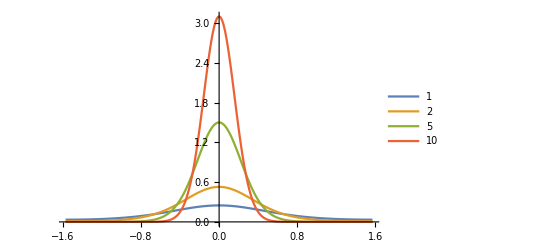

{3.09892,{θ→-5.81806×10^-20}}

vonmises.tsv

{3.09892,{θ→-5.81806×10^-20}}

-Graphics-

{3.09892,{θ→-5.81806×10^-20}}

-Graphics-

{{{-1.5708,0.0336558,0.00967353,0.000068118,6.38735×10^-9,0.0336558},{-1.5608,0.0336625,0.0096774,0.0000681861,6.40014×10^-9,0.0336625},{-1.5508,0.0336827,0.00968902,0.0000683909,6.43865×10^-9,0.0336827},{-1.5408,0.0337164,0.0097084,0.0000687336,6.50333×10^-9,0.0337164},{-1.5308,0.0337636,0.0097356,0.000069216,6.59494×10^-9,0.0337636},{-1.5208,0.0338243,0.00977067,0.0000698409,6.71456×10^-9,0.0338243},{-1.5108,0.0338987,0.00981366,0.0000706118,6.86361×10^-9,0.0338987},{-1.5008,0.0339867,0.00986468,0.0000715331,7.04389×10^-9,0.0339867},{-1.4908,0.0340884,0.00992383,0.0000726101,7.25758×10^-9,0.0340884},{-1.4808,0.0342039,0.00999121,0.000073849,7.50735×10^-9,0.0342039},{-1.4708,0.0343334,0.010067,0.0000752569,7.79634×10^-9,0.0343334},{-1.4608,0.0344768,0.0101513,0.0000768422,8.12825×10^-9,0.0344768},{-1.4508,0.0346344,0.0102443,0.0000786141,8.50743×10^-9,0.0346344},{-1.4408,0.0348061,0.0103461,0.0000805833,8.93897×10^-9,0.0348061},{-1.4308,0.0349923,0.0104571,0.0000827616,9.42877×10^-9,0.0349923},{-1.4208,0.035193,0.0105774,0.0000851623,9.98371×10^-9,0.035193},{-1.4108,0.0354084,0.0107073,0.0000878002,1.06118×10^-8,0.0354084},{-1.4008,0.0356386,0.0108469,0.0000906919,1.13223×10^-8,0.0356386},{-1.3908,0.0358838,0.0109967,0.0000938555,1.2126×10^-8,0.0358838},{-1.3808,0.0361443,0.011157,0.0000973115,1.30355×10^-8,0.0361443},{-1.3708,0.0364202,0.0113279,0.000101082,1.40653×10^-8,0.0364202},{-1.3608,0.0367117,0.01151,0.000105193,1.52325×10^-8,0.0367117},{-1.3508,0.037019,0.0117035,0.000109671,1.65569×10^-8,0.037019},{-1.3408,0.0373425,0.0119089,0.000114546,1.80617×10^-8,0.0373425},{-1.3308,0.0376822,0.0121266,0.000119853,1.97741×10^-8,0.0376822},{-1.3208,0.0380386,0.0123571,0.000125628,2.17257×10^-8,0.0380386},{-1.3108,0.0384118,0.0126007,0.000131913,2.39538×10^-8,0.0384118},{-1.3008,0.0388021,0.0128581,0.000138753,2.65023×10^-8,0.0388021},{-1.2908,0.0392099,0.0131298,0.000146199,2.94228×10^-8,0.0392099},{-1.2808,0.0396353,0.0134163,0.000154304,3.27759×10^-8,0.0396353},{-1.2708,0.0400788,0.0137182,0.000163133,3.66335×10^-8,0.0400788},{-1.2608,0.0405407,0.0140361,0.000172751,4.10806×10^-8,0.0405407},{-1.2508,0.0410212,0.0143708,0.000183234,4.62177×10^-8,0.0410212},{-1.2408,0.0415207,0.014723,0.000194665,5.21643×10^-8,0.0415207},{-1.2308,0.0420396,0.0150932,0.000207136,5.90623×10^-8,0.0420396},{-1.2208,0.0425782,0.0154825,0.00022075,6.70808×10^-8,0.0425782},{-1.2108,0.0431369,0.0158915,0.000235618,7.64214×10^-8,0.0431369},{-1.2008,0.0437161,0.0163211,0.000251866,8.73248×10^-8,0.0437161},{-1.1908,0.0443161,0.0167722,0.000269633,1.00079×10^-7,0.0443161},{-1.1808,0.0449374,0.0172458,0.000289071,1.15029×10^-7,0.0449374},{-1.1708,0.0455804,0.0177428,0.000310352,1.32589×10^-7,0.0455804},{-1.1608,0.0462454,0.0182643,0.000333664,1.53256×10^-7,0.0462454},{-1.1508,0.046933,0.0188115,0.000359217,1.77628×10^-7,0.046933},{-1.1408,0.0476435,0.0193854,0.000387243,2.06427×10^-7,0.0476435},{-1.1308,0.0483774,0.0199872,0.000418002,2.40521×10^-7,0.0483774},{-1.1208,0.0491351,0.0206182,0.000451778,2.80962×10^-7,0.0491351},{-1.1108,0.0499171,0.0212797,0.000488891,3.2902×10^-7,0.0499171},{-1.1008,0.0507238,0.0219731,0.000529695,3.86233×10^-7,0.0507238},{-1.0908,0.0515558,0.0226997,0.000574581,4.54465×10^-7,0.0515558},{-1.0808,0.0524134,0.0234612,0.000623986,5.35979×10^-7,0.0524134},{-1.0708,0.0532971,0.024259,0.000678395,6.33523×10^-7,0.0532971},{-1.0608,0.0542074,0.0250948,0.000738345,7.5044×10^-7,0.0542074},{-1.0508,0.0551449,0.0259703,0.000804435,8.90798×10^-7,0.0551449},{-1.0408,0.0561099,0.0268872,0.000877328,1.05955×10^-6,0.0561099},{-1.0308,0.0571029,0.0278473,0.000957762,1.26274×10^-6,0.0571029},{-1.0208,0.0581245,0.0288526,0.00104656,1.50773×10^-6,0.0581245},{-1.0108,0.0591751,0.0299051,0.00114462,1.80352×10^-6,0.0591751},{-1.0008,0.0602552,0.0310067,0.00125297,2.1611×10^-6,0.0602552},{-0.990796,0.0613653,0.0321597,0.00137271,2.59392×10^-6,0.0613653},{-0.980796,0.0625058,0.0333662,0.0015051,3.11839×10^-6,0.0625058},{-0.970796,0.0636772,0.0346285,0.00165152,3.75462×10^-6,0.0636772},{-0.960796,0.0648799,0.035949,0.0018135,4.52722×10^-6,0.0648799},{-0.950796,0.0661145,0.0373301,0.00199273,5.4663×10^-6,0.0661145},{-0.940796,0.0673813,0.0387744,0.00219109,6.60876×10^-6,0.0673813},{-0.930796,0.0686807,0.0402843,0.00241068,7.99977×10^-6,0.0686807},{-0.920796,0.0700133,0.0418627,0.0026538,9.69467×10^-6,0.0700133},{-0.910796,0.0713793,0.0435122,0.00292299,0.0000117612,0.0713793},{-0.900796,0.0727793,0.0452357,0.0032211,0.0000142825,0.0727793},{-0.890796,0.0742134,0.0470361,0.00355122,0.0000173602,0.0742134},{-0.880796,0.0756822,0.0489163,0.00391683,0.0000211186,0.0756822},{-0.870796,0.0771859,0.0508794,0.0043217,0.0000257103,0.0771859},{-0.860796,0.0787248,0.0529285,0.00477006,0.0000313217,0.0787248},{-0.850796,0.0802992,0.0550667,0.00526651,0.0000381806,0.0802992},{-0.840796,0.0819094,0.0572973,0.00581614,0.0000465658,0.0819094},{-0.830796,0.0835556,0.0596235,0.00642456,0.0000568177,0.0835556},{-0.820796,0.0852379,0.0620486,0.0070979,0.0000693518,0.0852379},{-0.810796,0.0869566,0.0645761,0.00784294,0.0000846749,0.0869566},{-0.800796,0.0887118,0.0672092,0.00866705,0.000103405,0.0887118},{-0.790796,0.0905034,0.0699514,0.00957835,0.000126293,0.0905034},{-0.780796,0.0923317,0.0728061,0.0105857,0.000154254,0.0923317},{-0.770796,0.0941965,0.0757768,0.0116988,0.000188399,0.0941965},{-0.760796,0.0960979,0.0788668,0.0129281,0.000230074,0.0960979},{-0.750796,0.0980358,0.0820796,0.0142853,0.000280914,0.0980358},{-0.740796,0.10001,0.0854186,0.0157827,0.000342893,0.10001},{-0.730796,0.10202,0.0888871,0.0174339,0.000418398,0.10202},{-0.720796,0.104066,0.0924883,0.0192538,0.000510305,0.104066},{-0.710796,0.106148,0.0962255,0.0212581,0.000622082,0.106148},{-0.700796,0.108265,0.100102,0.0234641,0.000757891,0.108265},{-0.690796,0.110417,0.10412,0.0258903,0.000922727,0.110417},{-0.680796,0.112603,0.108284,0.0285567,0.00112257,0.112603},{-0.670796,0.114822,0.112595,0.0314845,0.00136456,0.114822},{-0.660796,0.117075,0.117057,0.0346968,0.0016572,0.117075},{-0.650796,0.11936,0.121671,0.0382179,0.00201063,0.11936},{-0.640796,0.121677,0.12644,0.042074,0.00243683,0.121677},{-0.630796,0.124025,0.131367,0.0462928,0.00295002,0.124025},{-0.620796,0.126403,0.136452,0.0509036,0.00356693,0.126403},{-0.610796,0.128809,0.141697,0.0559374,0.00430728,0.128809},{-0.600796,0.131244,0.147104,0.061427,0.00519418,0.131244},{-0.590796,0.133705,0.152673,0.0674067,0.00625466,0.133705},{-0.580796,0.136192,0.158404,0.0739124,0.00752024,0.136192},{-0.570796,0.138702,0.164299,0.0809814,0.00902752,0.138702},{-0.560796,0.141236,0.170356,0.0886528,0.0108189,0.141236},{-0.550796,0.143791,0.176575,0.0969666,0.0129432,0.143791},{-0.540796,0.146366,0.182955,0.105964,0.0154567,0.146366},{-0.530796,0.148958,0.189494,0.115688,0.0184236,0.148958},{-0.520796,0.151567,0.19619,0.126181,0.0219172,0.151567},{-0.510796,0.154191,0.203041,0.137487,0.0260207,0.154191},{-0.500796,0.156827,0.210044,0.149649,0.030828,0.156827},{-0.490796,0.159474,0.217194,0.162712,0.0364449,0.159474},{-0.480796,0.16213,0.224488,0.176719,0.0429895,0.16213},{-0.470796,0.164792,0.231921,0.191711,0.0505934,0.164792},{-0.460796,0.167459,0.239487,0.207732,0.0594022,0.167459},{-0.450796,0.170127,0.24718,0.224819,0.0695764,0.170127},{-0.440796,0.172795,0.254994,0.243009,0.0812912,0.172795},{-0.430796,0.17546,0.262921,0.262338,0.0947371,0.17546},{-0.420796,0.17812,0.270953,0.282836,0.11012,0.17812},{-0.410796,0.180773,0.279082,0.304529,0.12766,0.180773},{-0.400796,0.183414,0.287298,0.327439,0.147591,0.183414},{-0.390796,0.186043,0.295591,0.351584,0.170159,0.186043},{-0.380796,0.188655,0.303952,0.376974,0.195623,0.188655},{-0.370796,0.191249,0.312368,0.403612,0.224247,0.191249},{-0.360796,0.193822,0.320827,0.431496,0.256302,0.193822},{-0.350796,0.19637,0.329318,0.460615,0.292061,0.19637},{-0.340796,0.19889,0.337827,0.490947,0.331793,0.19889},{-0.330796,0.201381,0.346341,0.522466,0.375762,0.201381},{-0.320796,0.203838,0.354845,0.555131,0.424217,0.203838},{-0.310796,0.20626,0.363325,0.588894,0.477388,0.20626},{-0.300796,0.208642,0.371766,0.623695,0.535479,0.208642},{-0.290796,0.210982,0.380152,0.659465,0.598662,0.210982},{-0.280796,0.213277,0.388467,0.696123,0.667066,0.213277},{-0.270796,0.215524,0.396696,0.733575,0.740775,0.215524},{-0.260796,0.21772,0.404822,0.771718,0.819813,0.21772},{-0.250796,0.219862,0.412827,0.810438,0.904144,0.219862},{-0.240796,0.221948,0.420696,0.84961,0.993658,0.221948},{-0.230796,0.223974,0.42841,0.889098,1.08817,0.223974},{-0.220796,0.225937,0.435954,0.928756,1.18741,0.225937},{-0.210796,0.227835,0.44331,0.968431,1.29103,0.227835},{-0.200796,0.229665,0.450461,1.00796,1.39857,0.229665},{-0.190796,0.231425,0.457391,1.04717,1.5095,0.231425},{-0.180796,0.233112,0.464082,1.08589,1.6232,0.233112},{-0.170796,0.234723,0.47052,1.12394,1.73894,0.234723},{-0.160796,0.236256,0.476687,1.16113,1.85593,0.236256},{-0.150796,0.237709,0.482568,1.19728,1.97329,0.237709},{-0.140796,0.23908,0.488149,1.2322,2.09006,0.23908},{-0.130796,0.240366,0.493416,1.2657,2.20526,0.240366},{-0.120796,0.241566,0.498353,1.29761,2.31784,0.241566},{-0.110796,0.242677,0.50295,1.32773,2.42672,0.242677},{-0.100796,0.243699,0.507193,1.35591,2.53082,0.243699},{-0.0907963,0.244629,0.511071,1.38198,2.62906,0.244629},{-0.0807963,0.245465,0.514573,1.40578,2.72039,0.245465},{-0.0707963,0.246208,0.517691,1.42717,2.80381,0.246208},{-0.0607963,0.246855,0.520415,1.44602,2.87836,0.246855},{-0.0507963,0.247405,0.522738,1.46221,2.94319,0.247405},{-0.0407963,0.247858,0.524654,1.47565,2.99752,0.247858},{-0.0307963,0.248213,0.526157,1.48624,3.04071,0.248213},{-0.0207963,0.248469,0.527244,1.49392,3.07224,0.248469},{-0.0107963,0.248626,0.527911,1.49865,3.09171,0.248626},{-0.000796327,0.248684,0.528155,1.50039,3.09888,0.248684},{0.00920367,0.248642,0.527978,1.49913,3.09368,0.248642},{0.0192037,0.248501,0.527378,1.49488,3.07615,0.248501},{0.0292037,0.248261,0.526359,1.48766,3.04653,0.248261},{0.0392037,0.247921,0.524921,1.47753,3.00516,0.247921},{0.0492037,0.247484,0.523071,1.46454,2.95256,0.247484},{0.0592037,0.246949,0.520812,1.44878,2.88936,0.246949},{0.0692037,0.246317,0.518151,1.43034,2.8163,0.246317},{0.0792037,0.24559,0.515096,1.40935,2.73424,0.24559},{0.0892037,0.244768,0.511654,1.38593,2.6441,0.244768},{0.0992037,0.243853,0.507835,1.36021,2.54689,0.243853},{0.109204,0.242846,0.503649,1.33236,2.44365,0.242846},{0.119204,0.241749,0.499109,1.30253,2.33546,0.241749},{0.129204,0.240563,0.494224,1.27089,2.2234,0.240563},{0.139204,0.239291,0.489009,1.23763,2.10854,0.239291},{0.149204,0.237933,0.483478,1.20293,1.99195,0.237933},{0.159204,0.236493,0.477643,1.16696,1.87462,0.236493},{0.169204,0.234973,0.47152,1.12993,1.75751,0.234973},{0.179204,0.233374,0.465125,1.092,1.64152,0.233374},{0.189204,0.231699,0.458473,1.05338,1.52744,0.231699},{0.199204,0.22995,0.45158,1.01423,1.41603,0.22995},{0.209204,0.228131,0.444463,0.974741,1.3079,0.228131},{0.219204,0.226244,0.437139,0.935078,1.20363,0.226244},{0.229204,0.224291,0.429624,0.895406,1.10367,0.224291},{0.239204,0.222275,0.421935,0.855881,1.00838,0.222275},{0.249204,0.220198,0.41409,0.81665,0.918057,0.220198},{0.259204,0.218065,0.406105,0.777849,0.832892,0.218065},{0.269204,0.215877,0.397998,0.739606,0.753006,0.215877},{0.279204,0.213638,0.389784,0.702037,0.678449,0.213638},{0.289204,0.211351,0.381481,0.665246,0.609204,0.211351},{0.299204,0.209017,0.373105,0.629329,0.545197,0.209017},{0.309204,0.206642,0.364672,0.594369,0.486306,0.206642},{0.319204,0.204227,0.356197,0.560436,0.432364,0.204227},{0.329204,0.201775,0.347696,0.527592,0.383173,0.201775},{0.339204,0.199289,0.339183,0.495889,0.338506,0.199289},{0.349204,0.196773,0.330672,0.465365,0.298116,0.196773},{0.359204,0.194229,0.322178,0.436051,0.261742,0.194229},{0.369204,0.19166,0.313712,0.40797,0.229115,0.19166},{0.379204,0.18907,0.305289,0.381133,0.199963,0.18907},{0.389204,0.18646,0.296919,0.355544,0.174014,0.18646},{0.399204,0.183834,0.288614,0.331202,0.151002,0.183834},{0.409204,0.181194,0.280385,0.308095,0.130668,0.181194},{0.419204,0.178543,0.272241,0.28621,0.112763,0.178543},{0.429204,0.175885,0.264193,0.265524,0.0970519,0.175885},{0.439204,0.17322,0.256249,0.246011,0.0833116,0.17322},{0.449204,0.170552,0.248416,0.227641,0.0713343,0.170552},{0.459204,0.167884,0.240704,0.210381,0.0609269,0.167884},{0.469204,0.165217,0.233117,0.194193,0.0519117,0.165217},{0.479204,0.162554,0.225663,0.179039,0.044126,0.162554},{0.489204,0.159897,0.218346,0.164878,0.0374218,0.159897},{0.499204,0.157248,0.211173,0.151668,0.0316655,0.157248},{0.509204,0.15461,0.204146,0.139365,0.0267366,0.15461},{0.519204,0.151984,0.197271,0.127926,0.0225276,0.151984},{0.529204,0.149373,0.19055,0.117306,0.0189427,0.149373},{0.539204,0.146777,0.183986,0.107463,0.015897,0.146777},{0.549204,0.1442,0.17758,0.0983527,0.0133159,0.1442},{0.559204,0.141642,0.171336,0.0899328,0.0111336,0.141642},{0.569204,0.139104,0.165253,0.0821619,0.00929262,0.139104},{0.579204,0.13659,0.159332,0.0749995,0.00774309,0.13659},{0.589204,0.134099,0.153575,0.0684067,0.00644161,0.134099},{0.599204,0.131634,0.14798,0.0623457,0.00535069,0.131634},{0.609204,0.129195,0.142547,0.0567804,0.00443807,0.129195},{0.619204,0.126784,0.137277,0.0516762,0.00367602,0.126784},{0.629204,0.124402,0.132166,0.0470001,0.00304085,0.124402},{0.639204,0.122049,0.127214,0.0427209,0.00251234,0.122049},{0.649204,0.119727,0.12242,0.038809,0.0020733,0.119727},{0.659204,0.117437,0.117781,0.0352363,0.00170914,0.117437},{0.669204,0.115179,0.113295,0.0319765,0.00140753,0.115179},{0.679204,0.112954,0.10896,0.0290049,0.00115808,0.112954},{0.689204,0.110763,0.104774,0.0262984,0.000952041,0.110763},{0.699204,0.108605,0.100732,0.0238353,0.000782058,0.108605},{0.709204,0.106483,0.0968335,0.0215955,0.000641984,0.106483},{0.719204,0.104395,0.0930743,0.0195602,0.000526679,0.104395},{0.729204,0.102344,0.0894516,0.0177121,0.000431855,0.102344},{0.739204,0.100328,0.0859622,0.016035,0.000353945,0.100328},{0.749204,0.0983478,0.0826029,0.014514,0.000289983,0.0983478},{0.759204,0.0964041,0.0793702,0.0131354,0.000237511,0.0964041},{0.769204,0.0944969,0.0762608,0.0118865,0.000194493,0.0944969},{0.779204,0.0926263,0.0732714,0.0107556,0.000159246,0.0926263},{0.789204,0.0907922,0.0703984,0.00973211,0.00013038,0.0907922},{0.799204,0.0889947,0.0676385,0.00880613,0.00010675,0.0889947},{0.809204,0.0872337,0.0649883,0.00796869,0.0000874121,0.0872337},{0.819204,0.0855092,0.0624442,0.00721158,0.000071591,0.0855092},{0.829204,0.0838211,0.060003,0.00652728,0.0000586492,0.0838211},{0.839204,0.0821692,0.0576613,0.00590895,0.0000480638,0.0821692},{0.849204,0.0805533,0.0554157,0.00535034,0.0000394059,0.0805533},{0.859204,0.0789732,0.053263,0.00484578,0.000032324,0.0789732},{0.869204,0.0774286,0.0511999,0.00439009,0.0000265304,0.0774286},{0.879204,0.0759193,0.0492234,0.00397858,0.0000217898,0.0759193},{0.889204,0.074445,0.0473301,0.00360698,0.0000179096,0.074445},{0.899204,0.0730054,0.0455173,0.00327144,0.0000147325,0.0730054},{0.909204,0.0716,0.0437817,0.00296846,0.00001213,0.0716},{0.919204,0.0702286,0.0421206,0.00269485,9.99697×10^-6,0.0702286},{0.929204,0.0688907,0.0405311,0.00244776,8.24777×10^-6,0.0688907},{0.939204,0.067586,0.0390104,0.00222459,6.81236×10^-6,0.067586},{0.949204,0.0663141,0.0375558,0.00202299,5.63358×10^-6,0.0663141},{0.959204,0.0650744,0.0361648,0.00184084,4.66477×10^-6,0.0650744},{0.969204,0.0638666,0.0348349,0.00167623,3.86783×10^-6,0.0638666},{0.979204,0.0626903,0.0335634,0.00152745,3.21166×10^-6,0.0626903},{0.989204,0.0615449,0.0323482,0.00139292,2.67084×10^-6,0.0615449},{0.999204,0.06043,0.0311869,0.00127124,2.22461×10^-6,0.06043},{1.0092,0.0593452,0.0300772,0.00116116,1.85602×10^-6,0.0593452},{1.0192,0.0582899,0.029017,0.00106153,1.55118×10^-6,0.0582899},{1.0292,0.0572637,0.0280043,0.000971321,1.29874×10^-6,0.0572637},{1.0392,0.0562661,0.0270371,0.000889613,1.08943×10^-6,0.0562661},{1.0492,0.0552967,0.0261135,0.00081557,9.15631×10^-7,0.0552967},{1.0592,0.0543549,0.0252315,0.000748443,7.71109×10^-7,0.0543549},{1.0692,0.0534403,0.0243895,0.000687557,6.50751×10^-7,0.0534403},{1.0792,0.0525523,0.0235858,0.000632303,5.50362×10^-7,0.0525523},{1.0892,0.0516906,0.0228186,0.000582135,4.66493×10^-7,0.0516906},{1.0992,0.0508546,0.0220865,0.000536559,3.96308×10^-7,0.0508546},{1.1092,0.0500439,0.0213879,0.000495133,3.37475×10^-7,0.0500439},{1.1192,0.049258,0.0207215,0.000457457,2.8807×10^-7,0.049258},{1.1292,0.0484965,0.0200857,0.000423171,2.46507×10^-7,0.0484965},{1.1392,0.0477588,0.0194793,0.000391952,2.11477×10^-7,0.0477588},{1.1492,0.0470446,0.0189011,0.000363509,1.81898×10^-7,0.0470446},{1.1592,0.0463534,0.0183497,0.000337578,1.56872×10^-7,0.0463534},{1.1692,0.0456848,0.0178242,0.000313924,1.35658×10^-7,0.0456848},{1.1792,0.0450383,0.0173233,0.000292333,1.17639×10^-7,0.0450383},{1.1892,0.0444136,0.0168461,0.000272612,1.02303×10^-7,0.0444136},{1.1992,0.0438102,0.0163914,0.00025459,8.9224×10^-8,0.0438102},{1.2092,0.0432277,0.0159585,0.00023811,7.80464×10^-8,0.0432277},{1.2192,0.0426658,0.0155463,0.000223031,6.84742×10^-8,0.0426658},{1.2292,0.042124,0.015154,0.000209225,6.02595×10^-8,0.042124},{1.2392,0.041602,0.0147807,0.000196579,5.31952×10^-8,0.041602},{1.2492,0.0410994,0.0144257,0.000184988,4.71072×10^-8,0.0410994},{1.2592,0.0406159,0.0140883,0.00017436,4.18497×10^-8,0.0406159},{1.2692,0.0401511,0.0137677,0.00016461,3.72999×10^-8,0.0401511},{1.2792,0.0397048,0.0134633,0.00015566,3.33545×10^-8,0.0397048},{1.2892,0.0392765,0.0131744,0.000147444,2.99261×10^-8,0.0392765},{1.2992,0.0388659,0.0129004,0.000139897,2.69411×10^-8,0.0388659},{1.3092,0.0384728,0.0126408,0.000132964,2.4337×10^-8,0.0384728},{1.3192,0.0380969,0.012395,0.000126594,2.2061×10^-8,0.0380969},{1.3292,0.0377379,0.0121625,0.00012074,2.0068×10^-8,0.0377379},{1.3392,0.0373955,0.0119428,0.000115362,1.83198×10^-8,0.0373955},{1.3492,0.0370695,0.0117354,0.00011042,1.67838×10^-8,0.0370695},{1.3592,0.0367596,0.01154,0.000105881,1.54323×10^-8,0.0367596},{1.3692,0.0364656,0.0113562,0.000101714,1.42415×10^-8,0.0364656},{1.3792,0.0361872,0.0111835,0.0000978904,1.3191×10^-8,0.0361872},{1.3892,0.0359243,0.0110216,0.0000943858,1.22634×10^-8,0.0359243},{1.3992,0.0356766,0.0108701,0.000091177,1.14437×10^-8,0.0356766},{1.4092,0.035444,0.0107288,0.0000882433,1.07192×10^-8,0.035444},{1.4192,0.0352263,0.0105974,0.0000855661,1.00786×10^-8,0.0352263},{1.4292,0.0350233,0.0104756,0.0000831287,9.5126×10^-9,0.0350233},{1.4392,0.0348348,0.0103632,0.0000809159,9.01291×10^-9,0.0348348},{1.4492,0.0346608,0.0102599,0.0000789142,8.57251×10^-9,0.0346608},{1.4592,0.0345009,0.0101655,0.0000771116,8.18535×10^-9,0.0345009},{1.4692,0.0343553,0.0100798,0.0000754973,7.84622×10^-9,0.0343553},{1.4792,0.0342236,0.0100027,0.0000740617,7.55066×10^-9,0.0342236},{1.4892,0.0341059,0.009934,0.0000727964,7.29487×10^-9,0.0341059},{1.4992,0.0340019,0.00987356,0.0000716941,7.07562×10^-9,0.0340019},{1.5092,0.0339118,0.00982125,0.0000707484,6.89018×10^-9,0.0339118},{1.5192,0.0338352,0.00977698,0.0000699538,6.73629×10^-9,0.0338352},{1.5292,0.0337723,0.00974066,0.0000693059,6.61208×10^-9,0.0337723},{1.5392,0.033723,0.00971221,0.000068801,6.51609×10^-9,0.033723},{1.5492,0.0336871,0.00969158,0.0000684362,6.44718×10^-9,0.0336871},{1.5592,0.0336648,0.00967873,0.0000682096,6.40454×10^-9,0.0336648},{1.5692,0.0336559,0.00967363,0.0000681197,6.38768×10^-9,0.0336559}}}

{3.09892,{θ→-5.81806×10^-20}}

-Graphics-

{{{-1.5708,0.0336558},{-1.5608,0.0336625},{-1.5508,0.0336827},{-1.5408,0.0337164},{-1.5308,0.0337636},{-1.5208,0.0338243},{-1.5108,0.0338987},{-1.5008,0.0339867},{-1.4908,0.0340884},{-1.4808,0.0342039},{-1.4708,0.0343334},{-1.4608,0.0344768},{-1.4508,0.0346344},{-1.4408,0.0348061},{-1.4308,0.0349923},{-1.4208,0.035193},{-1.4108,0.0354084},{-1.4008,0.0356386},{-1.3908,0.0358838},{-1.3808,0.0361443},{-1.3708,0.0364202},{-1.3608,0.0367117},{-1.3508,0.037019},{-1.3408,0.0373425},{-1.3308,0.0376822},{-1.3208,0.0380386},{-1.3108,0.0384118},{-1.3008,0.0388021},{-1.2908,0.0392099},{-1.2808,0.0396353},{-1.2708,0.0400788},{-1.2608,0.0405407},{-1.2508,0.0410212},{-1.2408,0.0415207},{-1.2308,0.0420396},{-1.2208,0.0425782},{-1.2108,0.0431369},{-1.2008,0.0437161},{-1.1908,0.0443161},{-1.1808,0.0449374},{-1.1708,0.0455804},{-1.1608,0.0462454},{-1.1508,0.046933},{-1.1408,0.0476435},{-1.1308,0.0483774},{-1.1208,0.0491351},{-1.1108,0.0499171},{-1.1008,0.0507238},{-1.0908,0.0515558},{-1.0808,0.0524134},{-1.0708,0.0532971},{-1.0608,0.0542074},{-1.0508,0.0551449},{-1.0408,0.0561099},{-1.0308,0.0571029},{-1.0208,0.0581245},{-1.0108,0.0591751},{-1.0008,0.0602552},{-0.990796,0.0613653},{-0.980796,0.0625058},{-0.970796,0.0636772},{-0.960796,0.0648799},{-0.950796,0.0661145},{-0.940796,0.0673813},{-0.930796,0.0686807},{-0.920796,0.0700133},{-0.910796,0.0713793},{-0.900796,0.0727793},{-0.890796,0.0742134},{-0.880796,0.0756822},{-0.870796,0.0771859},{-0.860796,0.0787248},{-0.850796,0.0802992},{-0.840796,0.0819094},{-0.830796,0.0835556},{-0.820796,0.0852379},{-0.810796,0.0869566},{-0.800796,0.0887118},{-0.790796,0.0905034},{-0.780796,0.0923317},{-0.770796,0.0941965},{-0.760796,0.0960979},{-0.750796,0.0980358},{-0.740796,0.10001},{-0.730796,0.10202},{-0.720796,0.104066},{-0.710796,0.106148},{-0.700796,0.108265},{-0.690796,0.110417},{-0.680796,0.112603},{-0.670796,0.114822},{-0.660796,0.117075},{-0.650796,0.11936},{-0.640796,0.121677},{-0.630796,0.124025},{-0.620796,0.126403},{-0.610796,0.128809},{-0.600796,0.131244},{-0.590796,0.133705},{-0.580796,0.136192},{-0.570796,0.138702},{-0.560796,0.141236},{-0.550796,0.143791},{-0.540796,0.146366},{-0.530796,0.148958},{-0.520796,0.151567},{-0.510796,0.154191},{-0.500796,0.156827},{-0.490796,0.159474},{-0.480796,0.16213},{-0.470796,0.164792},{-0.460796,0.167459},{-0.450796,0.170127},{-0.440796,0.172795},{-0.430796,0.17546},{-0.420796,0.17812},{-0.410796,0.180773},{-0.400796,0.183414},{-0.390796,0.186043},{-0.380796,0.188655},{-0.370796,0.191249},{-0.360796,0.193822},{-0.350796,0.19637},{-0.340796,0.19889},{-0.330796,0.201381},{-0.320796,0.203838},{-0.310796,0.20626},{-0.300796,0.208642},{-0.290796,0.210982},{-0.280796,0.213277},{-0.270796,0.215524},{-0.260796,0.21772},{-0.250796,0.219862},{-0.240796,0.221948},{-0.230796,0.223974},{-0.220796,0.225937},{-0.210796,0.227835},{-0.200796,0.229665},{-0.190796,0.231425},{-0.180796,0.233112},{-0.170796,0.234723},{-0.160796,0.236256},{-0.150796,0.237709},{-0.140796,0.23908},{-0.130796,0.240366},{-0.120796,0.241566},{-0.110796,0.242677},{-0.100796,0.243699},{-0.0907963,0.244629},{-0.0807963,0.245465},{-0.0707963,0.246208},{-0.0607963,0.246855},{-0.0507963,0.247405},{-0.0407963,0.247858},{-0.0307963,0.248213},{-0.0207963,0.248469},{-0.0107963,0.248626},{-0.000796327,0.248684},{0.00920367,0.248642},{0.0192037,0.248501},{0.0292037,0.248261},{0.0392037,0.247921},{0.0492037,0.247484},{0.0592037,0.246949},{0.0692037,0.246317},{0.0792037,0.24559},{0.0892037,0.244768},{0.0992037,0.243853},{0.109204,0.242846},{0.119204,0.241749},{0.129204,0.240563},{0.139204,0.239291},{0.149204,0.237933},{0.159204,0.236493},{0.169204,0.234973},{0.179204,0.233374},{0.189204,0.231699},{0.199204,0.22995},{0.209204,0.228131},{0.219204,0.226244},{0.229204,0.224291},{0.239204,0.222275},{0.249204,0.220198},{0.259204,0.218065},{0.269204,0.215877},{0.279204,0.213638},{0.289204,0.211351},{0.299204,0.209017},{0.309204,0.206642},{0.319204,0.204227},{0.329204,0.201775},{0.339204,0.199289},{0.349204,0.196773},{0.359204,0.194229},{0.369204,0.19166},{0.379204,0.18907},{0.389204,0.18646},{0.399204,0.183834},{0.409204,0.181194},{0.419204,0.178543},{0.429204,0.175885},{0.439204,0.17322},{0.449204,0.170552},{0.459204,0.167884},{0.469204,0.165217},{0.479204,0.162554},{0.489204,0.159897},{0.499204,0.157248},{0.509204,0.15461},{0.519204,0.151984},{0.529204,0.149373},{0.539204,0.146777},{0.549204,0.1442},{0.559204,0.141642},{0.569204,0.139104},{0.579204,0.13659},{0.589204,0.134099},{0.599204,0.131634},{0.609204,0.129195},{0.619204,0.126784},{0.629204,0.124402},{0.639204,0.122049},{0.649204,0.119727},{0.659204,0.117437},{0.669204,0.115179},{0.679204,0.112954},{0.689204,0.110763},{0.699204,0.108605},{0.709204,0.106483},{0.719204,0.104395},{0.729204,0.102344},{0.739204,0.100328},{0.749204,0.0983478},{0.759204,0.0964041},{0.769204,0.0944969},{0.779204,0.0926263},{0.789204,0.0907922},{0.799204,0.0889947},{0.809204,0.0872337},{0.819204,0.0855092},{0.829204,0.0838211},{0.839204,0.0821692},{0.849204,0.0805533},{0.859204,0.0789732},{0.869204,0.0774286},{0.879204,0.0759193},{0.889204,0.074445},{0.899204,0.0730054},{0.909204,0.0716},{0.919204,0.0702286},{0.929204,0.0688907},{0.939204,0.067586},{0.949204,0.0663141},{0.959204,0.0650744},{0.969204,0.0638666},{0.979204,0.0626903},{0.989204,0.0615449},{0.999204,0.06043},{1.0092,0.0593452},{1.0192,0.0582899},{1.0292,0.0572637},{1.0392,0.0562661},{1.0492,0.0552967},{1.0592,0.0543549},{1.0692,0.0534403},{1.0792,0.0525523},{1.0892,0.0516906},{1.0992,0.0508546},{1.1092,0.0500439},{1.1192,0.049258},{1.1292,0.0484965},{1.1392,0.0477588},{1.1492,0.0470446},{1.1592,0.0463534},{1.1692,0.0456848},{1.1792,0.0450383},{1.1892,0.0444136},{1.1992,0.0438102},{1.2092,0.0432277},{1.2192,0.0426658},{1.2292,0.042124},{1.2392,0.041602},{1.2492,0.0410994},{1.2592,0.0406159},{1.2692,0.0401511},{1.2792,0.0397048},{1.2892,0.0392765},{1.2992,0.0388659},{1.3092,0.0384728},{1.3192,0.0380969},{1.3292,0.0377379},{1.3392,0.0373955},{1.3492,0.0370695},{1.3592,0.0367596},{1.3692,0.0364656},{1.3792,0.0361872},{1.3892,0.0359243},{1.3992,0.0356766},{1.4092,0.035444},{1.4192,0.0352263},{1.4292,0.0350233},{1.4392,0.0348348},{1.4492,0.0346608},{1.4592,0.0345009},{1.4692,0.0343553},{1.4792,0.0342236},{1.4892,0.0341059},{1.4992,0.0340019},{1.5092,0.0339118},{1.5192,0.0338352},{1.5292,0.0337723},{1.5392,0.033723},{1.5492,0.0336871},{1.5592,0.0336648},{1.5692,0.0336559}},{{-1.5708,0.00967353},{-1.5608,0.0096774},{-1.5508,0.00968902},{-1.5408,0.0097084},{-1.5308,0.0097356},{-1.5208,0.00977067},{-1.5108,0.00981366},{-1.5008,0.00986468},{-1.4908,0.00992383},{-1.4808,0.00999121},{-1.4708,0.010067},{-1.4608,0.0101513},{-1.4508,0.0102443},{-1.4408,0.0103461},{-1.4308,0.0104571},{-1.4208,0.0105774},{-1.4108,0.0107073},{-1.4008,0.0108469},{-1.3908,0.0109967},{-1.3808,0.011157},{-1.3708,0.0113279},{-1.3608,0.01151},{-1.3508,0.0117035},{-1.3408,0.0119089},{-1.3308,0.0121266},{-1.3208,0.0123571},{-1.3108,0.0126007},{-1.3008,0.0128581},{-1.2908,0.0131298},{-1.2808,0.0134163},{-1.2708,0.0137182},{-1.2608,0.0140361},{-1.2508,0.0143708},{-1.2408,0.014723},{-1.2308,0.0150932},{-1.2208,0.0154825},{-1.2108,0.0158915},{-1.2008,0.0163211},{-1.1908,0.0167722},{-1.1808,0.0172458},{-1.1708,0.0177428},{-1.1608,0.0182643},{-1.1508,0.0188115},{-1.1408,0.0193854},{-1.1308,0.0199872},{-1.1208,0.0206182},{-1.1108,0.0212797},{-1.1008,0.0219731},{-1.0908,0.0226997},{-1.0808,0.0234612},{-1.0708,0.024259},{-1.0608,0.0250948},{-1.0508,0.0259703},{-1.0408,0.0268872},{-1.0308,0.0278473},{-1.0208,0.0288526},{-1.0108,0.0299051},{-1.0008,0.0310067},{-0.990796,0.0321597},{-0.980796,0.0333662},{-0.970796,0.0346285},{-0.960796,0.035949},{-0.950796,0.0373301},{-0.940796,0.0387744},{-0.930796,0.0402843},{-0.920796,0.0418627},{-0.910796,0.0435122},{-0.900796,0.0452357},{-0.890796,0.0470361},{-0.880796,0.0489163},{-0.870796,0.0508794},{-0.860796,0.0529285},{-0.850796,0.0550667},{-0.840796,0.0572973},{-0.830796,0.0596235},{-0.820796,0.0620486},{-0.810796,0.0645761},{-0.800796,0.0672092},{-0.790796,0.0699514},{-0.780796,0.0728061},{-0.770796,0.0757768},{-0.760796,0.0788668},{-0.750796,0.0820796},{-0.740796,0.0854186},{-0.730796,0.0888871},{-0.720796,0.0924883},{-0.710796,0.0962255},{-0.700796,0.100102},{-0.690796,0.10412},{-0.680796,0.108284},{-0.670796,0.112595},{-0.660796,0.117057},{-0.650796,0.121671},{-0.640796,0.12644},{-0.630796,0.131367},{-0.620796,0.136452},{-0.610796,0.141697},{-0.600796,0.147104},{-0.590796,0.152673},{-0.580796,0.158404},{-0.570796,0.164299},{-0.560796,0.170356},{-0.550796,0.176575},{-0.540796,0.182955},{-0.530796,0.189494},{-0.520796,0.19619},{-0.510796,0.203041},{-0.500796,0.210044},{-0.490796,0.217194},{-0.480796,0.224488},{-0.470796,0.231921},{-0.460796,0.239487},{-0.450796,0.24718},{-0.440796,0.254994},{-0.430796,0.262921},{-0.420796,0.270953},{-0.410796,0.279082},{-0.400796,0.287298},{-0.390796,0.295591},{-0.380796,0.303952},{-0.370796,0.312368},{-0.360796,0.320827},{-0.350796,0.329318},{-0.340796,0.337827},{-0.330796,0.346341},{-0.320796,0.354845},{-0.310796,0.363325},{-0.300796,0.371766},{-0.290796,0.380152},{-0.280796,0.388467},{-0.270796,0.396696},{-0.260796,0.404822},{-0.250796,0.412827},{-0.240796,0.420696},{-0.230796,0.42841},{-0.220796,0.435954},{-0.210796,0.44331},{-0.200796,0.450461},{-0.190796,0.457391},{-0.180796,0.464082},{-0.170796,0.47052},{-0.160796,0.476687},{-0.150796,0.482568},{-0.140796,0.488149},{-0.130796,0.493416},{-0.120796,0.498353},{-0.110796,0.50295},{-0.100796,0.507193},{-0.0907963,0.511071},{-0.0807963,0.514573},{-0.0707963,0.517691},{-0.0607963,0.520415},{-0.0507963,0.522738},{-0.0407963,0.524654},{-0.0307963,0.526157},{-0.0207963,0.527244},{-0.0107963,0.527911},{-0.000796327,0.528155},{0.00920367,0.527978},{0.0192037,0.527378},{0.0292037,0.526359},{0.0392037,0.524921},{0.0492037,0.523071},{0.0592037,0.520812},{0.0692037,0.518151},{0.0792037,0.515096},{0.0892037,0.511654},{0.0992037,0.507835},{0.109204,0.503649},{0.119204,0.499109},{0.129204,0.494224},{0.139204,0.489009},{0.149204,0.483478},{0.159204,0.477643},{0.169204,0.47152},{0.179204,0.465125},{0.189204,0.458473},{0.199204,0.45158},{0.209204,0.444463},{0.219204,0.437139},{0.229204,0.429624},{0.239204,0.421935},{0.249204,0.41409},{0.259204,0.406105},{0.269204,0.397998},{0.279204,0.389784},{0.289204,0.381481},{0.299204,0.373105},{0.309204,0.364672},{0.319204,0.356197},{0.329204,0.347696},{0.339204,0.339183},{0.349204,0.330672},{0.359204,0.322178},{0.369204,0.313712},{0.379204,0.305289},{0.389204,0.296919},{0.399204,0.288614},{0.409204,0.280385},{0.419204,0.272241},{0.429204,0.264193},{0.439204,0.256249},{0.449204,0.248416},{0.459204,0.240704},{0.469204,0.233117},{0.479204,0.225663},{0.489204,0.218346},{0.499204,0.211173},{0.509204,0.204146},{0.519204,0.197271},{0.529204,0.19055},{0.539204,0.183986},{0.549204,0.17758},{0.559204,0.171336},{0.569204,0.165253},{0.579204,0.159332},{0.589204,0.153575},{0.599204,0.14798},{0.609204,0.142547},{0.619204,0.137277},{0.629204,0.132166},{0.639204,0.127214},{0.649204,0.12242},{0.659204,0.117781},{0.669204,0.113295},{0.679204,0.10896},{0.689204,0.104774},{0.699204,0.100732},{0.709204,0.0968335},{0.719204,0.0930743},{0.729204,0.0894516},{0.739204,0.0859622},{0.749204,0.0826029},{0.759204,0.0793702},{0.769204,0.0762608},{0.779204,0.0732714},{0.789204,0.0703984},{0.799204,0.0676385},{0.809204,0.0649883},{0.819204,0.0624442},{0.829204,0.060003},{0.839204,0.0576613},{0.849204,0.0554157},{0.859204,0.053263},{0.869204,0.0511999},{0.879204,0.0492234},{0.889204,0.0473301},{0.899204,0.0455173},{0.909204,0.0437817},{0.919204,0.0421206},{0.929204,0.0405311},{0.939204,0.0390104},{0.949204,0.0375558},{0.959204,0.0361648},{0.969204,0.0348349},{0.979204,0.0335634},{0.989204,0.0323482},{0.999204,0.0311869},{1.0092,0.0300772},{1.0192,0.029017},{1.0292,0.0280043},{1.0392,0.0270371},{1.0492,0.0261135},{1.0592,0.0252315},{1.0692,0.0243895},{1.0792,0.0235858},{1.0892,0.0228186},{1.0992,0.0220865},{1.1092,0.0213879},{1.1192,0.0207215},{1.1292,0.0200857},{1.1392,0.0194793},{1.1492,0.0189011},{1.1592,0.0183497},{1.1692,0.0178242},{1.1792,0.0173233},{1.1892,0.0168461},{1.1992,0.0163914},{1.2092,0.0159585},{1.2192,0.0155463},{1.2292,0.015154},{1.2392,0.0147807},{1.2492,0.0144257},{1.2592,0.0140883},{1.2692,0.0137677},{1.2792,0.0134633},{1.2892,0.0131744},{1.2992,0.0129004},{1.3092,0.0126408},{1.3192,0.012395},{1.3292,0.0121625},{1.3392,0.0119428},{1.3492,0.0117354},{1.3592,0.01154},{1.3692,0.0113562},{1.3792,0.0111835},{1.3892,0.0110216},{1.3992,0.0108701},{1.4092,0.0107288},{1.4192,0.0105974},{1.4292,0.0104756},{1.4392,0.0103632},{1.4492,0.0102599},{1.4592,0.0101655},{1.4692,0.0100798},{1.4792,0.0100027},{1.4892,0.009934},{1.4992,0.00987356},{1.5092,0.00982125},{1.5192,0.00977698},{1.5292,0.00974066},{1.5392,0.00971221},{1.5492,0.00969158},{1.5592,0.00967873},{1.5692,0.00967363}},{{-1.5708,0.000068118},{-1.5608,0.0000681861},{-1.5508,0.0000683909},{-1.5408,0.0000687336},{-1.5308,0.000069216},{-1.5208,0.0000698409},{-1.5108,0.0000706118},{-1.5008,0.0000715331},{-1.4908,0.0000726101},{-1.4808,0.000073849},{-1.4708,0.0000752569},{-1.4608,0.0000768422},{-1.4508,0.0000786141},{-1.4408,0.0000805833},{-1.4308,0.0000827616},{-1.4208,0.0000851623},{-1.4108,0.0000878002},{-1.4008,0.0000906919},{-1.3908,0.0000938555},{-1.3808,0.0000973115},{-1.3708,0.000101082},{-1.3608,0.000105193},{-1.3508,0.000109671},{-1.3408,0.000114546},{-1.3308,0.000119853},{-1.3208,0.000125628},{-1.3108,0.000131913},{-1.3008,0.000138753},{-1.2908,0.000146199},{-1.2808,0.000154304},{-1.2708,0.000163133},{-1.2608,0.000172751},{-1.2508,0.000183234},{-1.2408,0.000194665},{-1.2308,0.000207136},{-1.2208,0.00022075},{-1.2108,0.000235618},{-1.2008,0.000251866},{-1.1908,0.000269633},{-1.1808,0.000289071},{-1.1708,0.000310352},{-1.1608,0.000333664},{-1.1508,0.000359217},{-1.1408,0.000387243},{-1.1308,0.000418002},{-1.1208,0.000451778},{-1.1108,0.000488891},{-1.1008,0.000529695},{-1.0908,0.000574581},{-1.0808,0.000623986},{-1.0708,0.000678395},{-1.0608,0.000738345},{-1.0508,0.000804435},{-1.0408,0.000877328},{-1.0308,0.000957762},{-1.0208,0.00104656},{-1.0108,0.00114462},{-1.0008,0.00125297},{-0.990796,0.00137271},{-0.980796,0.0015051},{-0.970796,0.00165152},{-0.960796,0.0018135},{-0.950796,0.00199273},{-0.940796,0.00219109},{-0.930796,0.00241068},{-0.920796,0.0026538},{-0.910796,0.00292299},{-0.900796,0.0032211},{-0.890796,0.00355122},{-0.880796,0.00391683},{-0.870796,0.0043217},{-0.860796,0.00477006},{-0.850796,0.00526651},{-0.840796,0.00581614},{-0.830796,0.00642456},{-0.820796,0.0070979},{-0.810796,0.00784294},{-0.800796,0.00866705},{-0.790796,0.00957835},{-0.780796,0.0105857},{-0.770796,0.0116988},{-0.760796,0.0129281},{-0.750796,0.0142853},{-0.740796,0.0157827},{-0.730796,0.0174339},{-0.720796,0.0192538},{-0.710796,0.0212581},{-0.700796,0.0234641},{-0.690796,0.0258903},{-0.680796,0.0285567},{-0.670796,0.0314845},{-0.660796,0.0346968},{-0.650796,0.0382179},{-0.640796,0.042074},{-0.630796,0.0462928},{-0.620796,0.0509036},{-0.610796,0.0559374},{-0.600796,0.061427},{-0.590796,0.0674067},{-0.580796,0.0739124},{-0.570796,0.0809814},{-0.560796,0.0886528},{-0.550796,0.0969666},{-0.540796,0.105964},{-0.530796,0.115688},{-0.520796,0.126181},{-0.510796,0.137487},{-0.500796,0.149649},{-0.490796,0.162712},{-0.480796,0.176719},{-0.470796,0.191711},{-0.460796,0.207732},{-0.450796,0.224819},{-0.440796,0.243009},{-0.430796,0.262338},{-0.420796,0.282836},{-0.410796,0.304529},{-0.400796,0.327439},{-0.390796,0.351584},{-0.380796,0.376974},{-0.370796,0.403612},{-0.360796,0.431496},{-0.350796,0.460615},{-0.340796,0.490947},{-0.330796,0.522466},{-0.320796,0.555131},{-0.310796,0.588894},{-0.300796,0.623695},{-0.290796,0.659465},{-0.280796,0.696123},{-0.270796,0.733575},{-0.260796,0.771718},{-0.250796,0.810438},{-0.240796,0.84961},{-0.230796,0.889098},{-0.220796,0.928756},{-0.210796,0.968431},{-0.200796,1.00796},{-0.190796,1.04717},{-0.180796,1.08589},{-0.170796,1.12394},{-0.160796,1.16113},{-0.150796,1.19728},{-0.140796,1.2322},{-0.130796,1.2657},{-0.120796,1.29761},{-0.110796,1.32773},{-0.100796,1.35591},{-0.0907963,1.38198},{-0.0807963,1.40578},{-0.0707963,1.42717},{-0.0607963,1.44602},{-0.0507963,1.46221},{-0.0407963,1.47565},{-0.0307963,1.48624},{-0.0207963,1.49392},{-0.0107963,1.49865},{-0.000796327,1.50039},{0.00920367,1.49913},{0.0192037,1.49488},{0.0292037,1.48766},{0.0392037,1.47753},{0.0492037,1.46454},{0.0592037,1.44878},{0.0692037,1.43034},{0.0792037,1.40935},{0.0892037,1.38593},{0.0992037,1.36021},{0.109204,1.33236},{0.119204,1.30253},{0.129204,1.27089},{0.139204,1.23763},{0.149204,1.20293},{0.159204,1.16696},{0.169204,1.12993},{0.179204,1.092},{0.189204,1.05338},{0.199204,1.01423},{0.209204,0.974741},{0.219204,0.935078},{0.229204,0.895406},{0.239204,0.855881},{0.249204,0.81665},{0.259204,0.777849},{0.269204,0.739606},{0.279204,0.702037},{0.289204,0.665246},{0.299204,0.629329},{0.309204,0.594369},{0.319204,0.560436},{0.329204,0.527592},{0.339204,0.495889},{0.349204,0.465365},{0.359204,0.436051},{0.369204,0.40797},{0.379204,0.381133},{0.389204,0.355544},{0.399204,0.331202},{0.409204,0.308095},{0.419204,0.28621},{0.429204,0.265524},{0.439204,0.246011},{0.449204,0.227641},{0.459204,0.210381},{0.469204,0.194193},{0.479204,0.179039},{0.489204,0.164878},{0.499204,0.151668},{0.509204,0.139365},{0.519204,0.127926},{0.529204,0.117306},{0.539204,0.107463},{0.549204,0.0983527},{0.559204,0.0899328},{0.569204,0.0821619},{0.579204,0.0749995},{0.589204,0.0684067},{0.599204,0.0623457},{0.609204,0.0567804},{0.619204,0.0516762},{0.629204,0.0470001},{0.639204,0.0427209},{0.649204,0.038809},{0.659204,0.0352363},{0.669204,0.0319765},{0.679204,0.0290049},{0.689204,0.0262984},{0.699204,0.0238353},{0.709204,0.0215955},{0.719204,0.0195602},{0.729204,0.0177121},{0.739204,0.016035},{0.749204,0.014514},{0.759204,0.0131354},{0.769204,0.0118865},{0.779204,0.0107556},{0.789204,0.00973211},{0.799204,0.00880613},{0.809204,0.00796869},{0.819204,0.00721158},{0.829204,0.00652728},{0.839204,0.00590895},{0.849204,0.00535034},{0.859204,0.00484578},{0.869204,0.00439009},{0.879204,0.00397858},{0.889204,0.00360698},{0.899204,0.00327144},{0.909204,0.00296846},{0.919204,0.00269485},{0.929204,0.00244776},{0.939204,0.00222459},{0.949204,0.00202299},{0.959204,0.00184084},{0.969204,0.00167623},{0.979204,0.00152745},{0.989204,0.00139292},{0.999204,0.00127124},{1.0092,0.00116116},{1.0192,0.00106153},{1.0292,0.000971321},{1.0392,0.000889613},{1.0492,0.00081557},{1.0592,0.000748443},{1.0692,0.000687557},{1.0792,0.000632303},{1.0892,0.000582135},{1.0992,0.000536559},{1.1092,0.000495133},{1.1192,0.000457457},{1.1292,0.000423171},{1.1392,0.000391952},{1.1492,0.000363509},{1.1592,0.000337578},{1.1692,0.000313924},{1.1792,0.000292333},{1.1892,0.000272612},{1.1992,0.00025459},{1.2092,0.00023811},{1.2192,0.000223031},{1.2292,0.000209225},{1.2392,0.000196579},{1.2492,0.000184988},{1.2592,0.00017436},{1.2692,0.00016461},{1.2792,0.00015566},{1.2892,0.000147444},{1.2992,0.000139897},{1.3092,0.000132964},{1.3192,0.000126594},{1.3292,0.00012074},{1.3392,0.000115362},{1.3492,0.00011042},{1.3592,0.000105881},{1.3692,0.000101714},{1.3792,0.0000978904},{1.3892,0.0000943858},{1.3992,0.000091177},{1.4092,0.0000882433},{1.4192,0.0000855661},{1.4292,0.0000831287},{1.4392,0.0000809159},{1.4492,0.0000789142},{1.4592,0.0000771116},{1.4692,0.0000754973},{1.4792,0.0000740617},{1.4892,0.0000727964},{1.4992,0.0000716941},{1.5092,0.0000707484},{1.5192,0.0000699538},{1.5292,0.0000693059},{1.5392,0.000068801},{1.5492,0.0000684362},{1.5592,0.0000682096},{1.5692,0.0000681197}},{{-1.5708,6.38735×10^-9},{-1.5608,6.40014×10^-9},{-1.5508,6.43865×10^-9},{-1.5408,6.50333×10^-9},{-1.5308,6.59494×10^-9},{-1.5208,6.71456×10^-9},{-1.5108,6.86361×10^-9},{-1.5008,7.04389×10^-9},{-1.4908,7.25758×10^-9},{-1.4808,7.50735×10^-9},{-1.4708,7.79634×10^-9},{-1.4608,8.12825×10^-9},{-1.4508,8.50743×10^-9},{-1.4408,8.93897×10^-9},{-1.4308,9.42877×10^-9},{-1.4208,9.98371×10^-9},{-1.4108,1.06118×10^-8},{-1.4008,1.13223×10^-8},{-1.3908,1.2126×10^-8},{-1.3808,1.30355×10^-8},{-1.3708,1.40653×10^-8},{-1.3608,1.52325×10^-8},{-1.3508,1.65569×10^-8},{-1.3408,1.80617×10^-8},{-1.3308,1.97741×10^-8},{-1.3208,2.17257×10^-8},{-1.3108,2.39538×10^-8},{-1.3008,2.65023×10^-8},{-1.2908,2.94228×10^-8},{-1.2808,3.27759×10^-8},{-1.2708,3.66335×10^-8},{-1.2608,4.10806×10^-8},{-1.2508,4.62177×10^-8},{-1.2408,5.21643×10^-8},{-1.2308,5.90623×10^-8},{-1.2208,6.70808×10^-8},{-1.2108,7.64214×10^-8},{-1.2008,8.73248×10^-8},{-1.1908,1.00079×10^-7},{-1.1808,1.15029×10^-7},{-1.1708,1.32589×10^-7},{-1.1608,1.53256×10^-7},{-1.1508,1.77628×10^-7},{-1.1408,2.06427×10^-7},{-1.1308,2.40521×10^-7},{-1.1208,2.80962×10^-7},{-1.1108,3.2902×10^-7},{-1.1008,3.86233×10^-7},{-1.0908,4.54465×10^-7},{-1.0808,5.35979×10^-7},{-1.0708,6.33523×10^-7},{-1.0608,7.5044×10^-7},{-1.0508,8.90798×10^-7},{-1.0408,1.05955×10^-6},{-1.0308,1.26274×10^-6},{-1.0208,1.50773×10^-6},{-1.0108,1.80352×10^-6},{-1.0008,2.1611×10^-6},{-0.990796,2.59392×10^-6},{-0.980796,3.11839×10^-6},{-0.970796,3.75462×10^-6},{-0.960796,4.52722×10^-6},{-0.950796,5.4663×10^-6},{-0.940796,6.60876×10^-6},{-0.930796,7.99977×10^-6},{-0.920796,9.69467×10^-6},{-0.910796,0.0000117612},{-0.900796,0.0000142825},{-0.890796,0.0000173602},{-0.880796,0.0000211186},{-0.870796,0.0000257103},{-0.860796,0.0000313217},{-0.850796,0.0000381806},{-0.840796,0.0000465658},{-0.830796,0.0000568177},{-0.820796,0.0000693518},{-0.810796,0.0000846749},{-0.800796,0.000103405},{-0.790796,0.000126293},{-0.780796,0.000154254},{-0.770796,0.000188399},{-0.760796,0.000230074},{-0.750796,0.000280914},{-0.740796,0.000342893},{-0.730796,0.000418398},{-0.720796,0.000510305},{-0.710796,0.000622082},{-0.700796,0.000757891},{-0.690796,0.000922727},{-0.680796,0.00112257},{-0.670796,0.00136456},{-0.660796,0.0016572},{-0.650796,0.00201063},{-0.640796,0.00243683},{-0.630796,0.00295002},{-0.620796,0.00356693},{-0.610796,0.00430728},{-0.600796,0.00519418},{-0.590796,0.00625466},{-0.580796,0.00752024},{-0.570796,0.00902752},{-0.560796,0.0108189},{-0.550796,0.0129432},{-0.540796,0.0154567},{-0.530796,0.0184236},{-0.520796,0.0219172},{-0.510796,0.0260207},{-0.500796,0.030828},{-0.490796,0.0364449},{-0.480796,0.0429895},{-0.470796,0.0505934},{-0.460796,0.0594022},{-0.450796,0.0695764},{-0.440796,0.0812912},{-0.430796,0.0947371},{-0.420796,0.11012},{-0.410796,0.12766},{-0.400796,0.147591},{-0.390796,0.170159},{-0.380796,0.195623},{-0.370796,0.224247},{-0.360796,0.256302},{-0.350796,0.292061},{-0.340796,0.331793},{-0.330796,0.375762},{-0.320796,0.424217},{-0.310796,0.477388},{-0.300796,0.535479},{-0.290796,0.598662},{-0.280796,0.667066},{-0.270796,0.740775},{-0.260796,0.819813},{-0.250796,0.904144},{-0.240796,0.993658},{-0.230796,1.08817},{-0.220796,1.18741},{-0.210796,1.29103},{-0.200796,1.39857},{-0.190796,1.5095},{-0.180796,1.6232},{-0.170796,1.73894},{-0.160796,1.85593},{-0.150796,1.97329},{-0.140796,2.09006},{-0.130796,2.20526},{-0.120796,2.31784},{-0.110796,2.42672},{-0.100796,2.53082},{-0.0907963,2.62906},{-0.0807963,2.72039},{-0.0707963,2.80381},{-0.0607963,2.87836},{-0.0507963,2.94319},{-0.0407963,2.99752},{-0.0307963,3.04071},{-0.0207963,3.07224},{-0.0107963,3.09171},{-0.000796327,3.09888},{0.00920367,3.09368},{0.0192037,3.07615},{0.0292037,3.04653},{0.0392037,3.00516},{0.0492037,2.95256},{0.0592037,2.88936},{0.0692037,2.8163},{0.0792037,2.73424},{0.0892037,2.6441},{0.0992037,2.54689},{0.109204,2.44365},{0.119204,2.33546},{0.129204,2.2234},{0.139204,2.10854},{0.149204,1.99195},{0.159204,1.87462},{0.169204,1.75751},{0.179204,1.64152},{0.189204,1.52744},{0.199204,1.41603},{0.209204,1.3079},{0.219204,1.20363},{0.229204,1.10367},{0.239204,1.00838},{0.249204,0.918057},{0.259204,0.832892},{0.269204,0.753006},{0.279204,0.678449},{0.289204,0.609204},{0.299204,0.545197},{0.309204,0.486306},{0.319204,0.432364},{0.329204,0.383173},{0.339204,0.338506},{0.349204,0.298116},{0.359204,0.261742},{0.369204,0.229115},{0.379204,0.199963},{0.389204,0.174014},{0.399204,0.151002},{0.409204,0.130668},{0.419204,0.112763},{0.429204,0.0970519},{0.439204,0.0833116},{0.449204,0.0713343},{0.459204,0.0609269},{0.469204,0.0519117},{0.479204,0.044126},{0.489204,0.0374218},{0.499204,0.0316655},{0.509204,0.0267366},{0.519204,0.0225276},{0.529204,0.0189427},{0.539204,0.015897},{0.549204,0.0133159},{0.559204,0.0111336},{0.569204,0.00929262},{0.579204,0.00774309},{0.589204,0.00644161},{0.599204,0.00535069},{0.609204,0.00443807},{0.619204,0.00367602},{0.629204,0.00304085},{0.639204,0.00251234},{0.649204,0.0020733},{0.659204,0.00170914},{0.669204,0.00140753},{0.679204,0.00115808},{0.689204,0.000952041},{0.699204,0.000782058},{0.709204,0.000641984},{0.719204,0.000526679},{0.729204,0.000431855},{0.739204,0.000353945},{0.749204,0.000289983},{0.759204,0.000237511},{0.769204,0.000194493},{0.779204,0.000159246},{0.789204,0.00013038},{0.799204,0.00010675},{0.809204,0.0000874121},{0.819204,0.000071591},{0.829204,0.0000586492},{0.839204,0.0000480638},{0.849204,0.0000394059},{0.859204,0.000032324},{0.869204,0.0000265304},{0.879204,0.0000217898},{0.889204,0.0000179096},{0.899204,0.0000147325},{0.909204,0.00001213},{0.919204,9.99697×10^-6},{0.929204,8.24777×10^-6},{0.939204,6.81236×10^-6},{0.949204,5.63358×10^-6},{0.959204,4.66477×10^-6},{0.969204,3.86783×10^-6},{0.979204,3.21166×10^-6},{0.989204,2.67084×10^-6},{0.999204,2.22461×10^-6},{1.0092,1.85602×10^-6},{1.0192,1.55118×10^-6},{1.0292,1.29874×10^-6},{1.0392,1.08943×10^-6},{1.0492,9.15631×10^-7},{1.0592,7.71109×10^-7},{1.0692,6.50751×10^-7},{1.0792,5.50362×10^-7},{1.0892,4.66493×10^-7},{1.0992,3.96308×10^-7},{1.1092,3.37475×10^-7},{1.1192,2.8807×10^-7},{1.1292,2.46507×10^-7},{1.1392,2.11477×10^-7},{1.1492,1.81898×10^-7},{1.1592,1.56872×10^-7},{1.1692,1.35658×10^-7},{1.1792,1.17639×10^-7},{1.1892,1.02303×10^-7},{1.1992,8.9224×10^-8},{1.2092,7.80464×10^-8},{1.2192,6.84742×10^-8},{1.2292,6.02595×10^-8},{1.2392,5.31952×10^-8},{1.2492,4.71072×10^-8},{1.2592,4.18497×10^-8},{1.2692,3.72999×10^-8},{1.2792,3.33545×10^-8},{1.2892,2.99261×10^-8},{1.2992,2.69411×10^-8},{1.3092,2.4337×10^-8},{1.3192,2.2061×10^-8},{1.3292,2.0068×10^-8},{1.3392,1.83198×10^-8},{1.3492,1.67838×10^-8},{1.3592,1.54323×10^-8},{1.3692,1.42415×10^-8},{1.3792,1.3191×10^-8},{1.3892,1.22634×10^-8},{1.3992,1.14437×10^-8},{1.4092,1.07192×10^-8},{1.4192,1.00786×10^-8},{1.4292,9.5126×10^-9},{1.4392,9.01291×10^-9},{1.4492,8.57251×10^-9},{1.4592,8.18535×10^-9},{1.4692,7.84622×10^-9},{1.4792,7.55066×10^-9},{1.4892,7.29487×10^-9},{1.4992,7.07562×10^-9},{1.5092,6.89018×10^-9},{1.5192,6.73629×10^-9},{1.5292,6.61208×10^-9},{1.5392,6.51609×10^-9},{1.5492,6.44718×10^-9},{1.5592,6.40454×10^-9},{1.5692,6.38768×10^-9}}}

{3.09892,{θ→-5.81806×10^-20}}

-Graphics-

-Graphics-

{3.09892,{θ→-5.81806×10^-20}}

```mathematica
ρip=Join[Table[{θ,ipodfn[1.0]/intn,ipodfn[2.0]/intn,ipodfn[5.0]/intn,ipodfn[10.0]/intn},{θ,-π/2,π/2,0.01}]];
ρip1=Join[Table[{θ,ipodfn[1.0]/intn},{θ,-π/2,π/2,0.01}]];
ρip2=Join[Table[{θ,ipodfn[2.0]/intn},{θ,-π/2,π/2,0.01}]];
ρip3=Join[Table[{θ,ipodfn[5.0]/intn},{θ,-π/2,π/2,0.01}]];
ρip4=Join[Table[{θ,ipodfn[10.0]/intn},{θ,-π/2,π/2,0.01}]];
lpi=ListPlot[{ρip1,ρip2,ρip3,ρip4},Joined->True,PlotRange->{{-π/2,π/2},Full},PlotLegends-> {1,2,5,10}]
FindMaximum[ipodf[a]/int,θ]
Export["vonmises.tsv",ρip]
```

```mathematica
(*rotational simmetry around θ=0; von mises distribution around mean direction θ=0;numerical solution*)
```

```mathematica
ipodfn[b_]:=N[4*Sqrt[b/(2π)]*Exp[b*(Cos[2*θ]+1)]/(π^(-1/2)*(2*Sqrt[2*b]+2*Sqrt[2*b]^3/3+∑_(j=3)^60 Sqrt[2*b]^(2*j-1)/(0.5*(2*j-1)*Factorial[(j-1)])))];
```

12.5664

1.

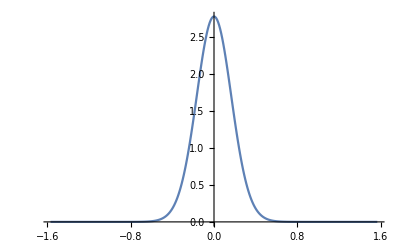

{2.78,{θ→-1.03388×10^-11}}

```mathematica
intn=N[∫_0^π ∫_0^(2π) ipodfn[a]*Sin[θ]ⅆϕⅆθ]
N[∫_0^π ∫_0^(2π) (ipodfn[a]/intn)*Sin[θ]ⅆϕⅆθ]
ρipn=Join[Table[{θ,ipodfn[a]/intn},{θ,-π/2,π/2,0.01}]];
lpin=ListPlot[{ρipn},Joined->True,PlotRange->{{-π/2,π/2},Full}]
FindMaximum[ipodfn[a]/int,θ]
```

```mathematica
(*graphical 3D visualisation*)
```

```mathematica
surf=(ipodf/int)*n;
N[surf]//MatrixForm
```

(0.0795775 ipodf Cos[ϕ] Sin[θ]
0.0795775 ipodf Sin[θ] Sin[ϕ]
0.0795775 ipodf Cos[θ])

```mathematica
g1=SphericalPlot3D[{{((ipodf[0.001])*n).n}},θ,ϕ,PlotRange->{Full,Full,Full},ViewPoint->Front,Mesh->None,MaxRecursion->4];
g2 =SphericalPlot3D[{{((ipodf[1.0])*n).n}},θ,ϕ,PlotRange->{Full,Full,Full},ViewPoint->Front,Mesh->None,MaxRecursion->4];
g3 =SphericalPlot3D[{{((ipodf[2.0])*n).n}},θ,ϕ,PlotRange->{Full,Full,Full},ViewPoint->Front,Mesh->None,MaxRecursion->4];
g4 =SphericalPlot3D[{{((ipodf[5.0])*n).n}},θ,ϕ,PlotRange->{Full,Full,Full},ViewPoint->Front,Mesh->None,MaxRecursion->4];
g5 =SphericalPlot3D[{{((ipodf[10.0])*n).n}},θ,ϕ,PlotRange->{Full,Full,Full},ViewPoint->Front,Mesh->None,MaxRecursion->4];
GraphicsRow[{g1,g2,g3,g4,g5},AspectRatio->Full,BaselinePosition->Bottom,Frame->None]
```

-Graphics-

```mathematica
Plot3D[(ipodf[a]/int)*(Sqrt[n.n]),{ϕ,-π/2,π/2},{θ,0,π},PlotRange->Full]
```

-Graphics3D-

```mathematica
N[Sqrt[2*1]]
```

1.41421

```mathematica
N[2*Sqrt[2*1]]
```

2.82843

```mathematica
N[(2/3)*Sqrt[2*1]^3]
```

1.88562

```mathematica
N[∑_(j=3)^60 Sqrt[2*1]^(2*j-1)/(0.5*(2*j-1)*Factorial[(j-1)])]
```

1.97364

```mathematica
N[Erfi[Sqrt[2*10]]]
```

6.28694×10^7